```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
list=FileNames["./output/ctags*.out","",2];
```

```mathematica
data=Import["./output/ctags"<>ToString[100]<>".out","Table"];
```

```mathematica
Sort[DeleteDuplicates[Flatten@data]] //Last
```

144

```mathematica
M=75^2;
```

```mathematica
hue[x_]:=If[x==0,{0,0,0},{Piecewise[{{2-6x, 1/6<x≤2/6}, {0, 2/6<x≤4/6}, {6x-4, 4/6<x≤5/6}, {1, True}}],Piecewise[{{6x, 0/6<x≤1/6}, {1, 1/6<x≤3/6}, {4-6x, 3/6<x≤4/6}, {0, True}}],Piecewise[{{0, 0/6<x≤2/6}, {6x-2, 2/6<x≤3/6}, {6-6x, 5/6<x≤6/6}, {1, True}}]}];
```

```mathematica
permute=RandomSample[Range[M]];
```

```mathematica
changes=Table[i-> permute[[i]],{i,1,M}];
```

```mathematica
permute2=RandomSample[Range[M]];
changes2=Table[i-> permute2[[i]],{i,1,M}];
```

```mathematica
Clear[ColorsReplace]
```

```mathematica
ColorsReplace[x_]:=(ColorsReplace[x]={1,1,1}(0.6(x/.changes)/M+If[x==0,0,0.4])-{0.3,0.3,0.3}hue[(x/.changes2)/M])
```

```mathematica
ColorsReplace[1]
```

{0.3832,0.43712,0.6832}

```mathematica
data=Import["./output/ctags"<>ToString[700]<>".out","Table"];
```

```mathematica
Image[Map[ColorsReplace,data[[;;,;;]],{2}]ᵀ]
```

-Graphics-

```mathematica
data=Import["./output/ctags700.sout","Table"];
```

```mathematica
contsI=Import["./output/contactM701.out","Table"];
Image@contsI
```

-Graphics-

```mathematica
σ=4; proc=0.05;Counts[arr_]:=Module[{uni=DeleteDuplicates[arr]},{Map[Count[arr,#]&,uni],uni}ᵀ];
Replacement[arr_]:=Module[{c=Counts[Flatten@arr]},Sort[c,#1[[1]]>#2[[1]]&]ᵀ[[2,1]]];
RepConts[arr_]:=If[Total[Flatten@arr]<(σ+1)^2 proc,0,1];
```

```mathematica
If[σ==0,
indexes=data;
conts=contsI,
indexes=Table[Replacement[data[[i;;i+σ,j;;j+σ]]],{i,1,Dimensions[data][[1]]-σ,σ+1},{j,1,Dimensions[data][[2]]-σ,σ+1}];
conts=Table[RepConts[contsI[[i;;i+σ,j;;j+σ]]] ,{i,1,Dimensions[contsI][[1]]-σ,σ+1},{j,1,Dimensions[contsI][[2]]-σ,σ+1}]
];
```

```mathematica
Image[Map[ColorsReplace,indexes,{2}]ᵀ]
```

-Graphics-

```mathematica
{Lx,Ly}=Dimensions[indexes];
```

```mathematica
Invert[x_]:={1,1,1}-x;
```

```mathematica
cells=Map[ColorsReplace,indexes,{2}];
```

```mathematica
BorderQ[x_,i_,j_]:=Module[{n,m,Q=1},
For[n=-1,n≤1,For[m=-1,m≤1,
If[x⟦i+n,j+m⟧≠x⟦i,j⟧,Q=0]
 m++]n++]; Q];
```

```mathematica
outerConts=ArrayPad[Table[If[conts⟦i,j⟧==1,1-BorderQ[indexes,i,j],0],{i,2,Lx-1},{j,2,Ly-1}],1];
```

```mathematica
Image[ConstantArray[{1,0,0},{Lx,Ly}]outerConts+cells Map[(1-#)&,outerConts]]
```

-Graphics-

```mathematica
{Lx,Ly}
```

{160,160}

```mathematica
(*indexes=Table[If[i<16&&j<160,1,0],{i,1,64},{j,1,320}];
cells=Map[ColorsReplace,indexes,{2}];
outerConts=Table[If[i==15&&j==159,1,0],{i,1,64},{j,1,320}];
{Lx,Ly}=Dimensions[indexes]*)
```

```mathematica
ThisCell[ind_,x_]:=Map[If[ind==#,1,0]&,x,{2}];NearContactQ[ind_,cellx_,contx_]:=Module[{this,n,m},this=mask ThisCell[ind,cellx]contx;Max@Table[If[this⟦n+R+1,m+R+1⟧==1,1,0],{n,-R,R},{m,-R,R}]];
```

```mathematica
borders=ArrayPad[Table[BorderQ[cells,i,j],{i,2,First@Dimensions[cells]-1},{j,2,Dimensions[cells][[2]]-1}],1];
```

```mathematica
niceCells=(ConstantArray[{1,0,0},{Lx,Ly}]outerConts+cells Map[(1-#)&,outerConts]);
```

```mathematica
leaveX=32 5; leaveY = 32 5; shiftx=0;shifty=0;
 cutX=Floor[(First@Dimensions[indexes]-leaveX)/2]+1;
cutY=Floor[(Last@Dimensions[indexes]-leaveY)/2]+1;
halfX=If[OddQ[First@Dimensions[indexes]-leaveX],1,0];
halfY=If[OddQ[Last@Dimensions[indexes]-leaveY],1,0];
Image[(niceCells borders+niceCells Map[0.7(1-#)&,borders])⟦cutX+shiftx;;-cutX+shiftx-halfX,cutY+shifty;;-cutY+shifty-halfY⟧]
```

-Graphics-

```mathematica
ind=indexes⟦cutX+shiftx;;-cutX+shiftx-halfX,cutY+shifty;;-cutY+shifty-halfY⟧;
```

```mathematica
endsCut=outerConts⟦cutX+shiftx;;-cutX+shiftx-halfX,cutY+shifty;;-cutY+shifty-halfY⟧ᵀ;
```

```mathematica
indCut=Map[If[#≠0,1,0]&,indexes⟦cutX+shiftx;;-cutX+shiftx-halfX,cutY+shifty;;-cutY+shifty-halfY⟧,{2}]ᵀ;
```

```mathematica
vertBord=ArrayPad[Map[If[#≠0,1,0]&,ind⟦2;;⟧-ind⟦;;-2⟧,{2}]Map[If[#≠0,1,0]&,ind⟦2;;⟧,{2}]Map[If[#≠0,1,0]&,ind⟦;;-2⟧,{2}],{{1,0},{0,0}}]ᵀ;;vert=ArrayPad[Map[If[#==0,1,0]&,ind⟦2;;⟧-ind⟦;;-2⟧,{2}]Map[If[#≠0,1,0]&,ind⟦2;;⟧,{2}],{{1,0},{0,0}}]ᵀ+2vertBord+vertBord endsCut;
```

```mathematica
horBord=ArrayPad[Map[If[#≠0,1,0]&,ind⟦;;,2;;⟧-ind⟦;;,;;-2⟧,{2}]Map[If[#≠0,1,0]&,ind⟦;;,2;;⟧,{2}]Map[If[#≠0,1,0]&,ind⟦;;,;;-2⟧,{2}],{{0,0},{1,0}}]ᵀ;
hor=ArrayPad[Map[If[#==0,1,0]&,ind⟦;;,2;;⟧-ind⟦;;,;;-2⟧,{2}]Map[If[#≠0,1,0]&,ind⟦;;,2;;⟧,{2}],{{0,0},{1,0}}]ᵀ+2 horBord+horBord endsCut;
```

```mathematica
Image[((vertᵀ)~Join~(horᵀ))/3]
```

-Graphics-

```mathematica
Dimensions@(vert)
```

{160,160}

```mathematica
Gather[Flatten@endsCut][[;;,1]]
```

{0,1}

```mathematica
Gather[Flatten@indCut][[;;,1]]
```

{0,1}

```mathematica
Gather[Flatten@hor][[;;,1]]
```

{0,1,3,2}

```mathematica
filename="./maps/cells.bin";
DeleteFile[filename];
BinaryWrite[filename,Dimensions@indCut,"Integer32"]; 
BinaryWrite[filename,Flatten@(indCutᵀ),"Integer8"];Close[filename]
```

./maps/cells.bin

```mathematica
filename="./maps/dx.bin";
DeleteFile[filename];
BinaryWrite[filename,Dimensions@vert,"Integer32"]; 
BinaryWrite[filename,Flatten@(vertᵀ),"Integer8"];Close[filename]
```

./maps/dx.bin

```mathematica
filename="./maps/dy.bin";
DeleteFile[filename];
BinaryWrite[filename,Dimensions@hor,"Integer32"]; 
BinaryWrite[filename,Flatten@(horᵀ),"Integer8"]; Close[filename]
```

./maps/dy.bin

```mathematica
filename="./maps/na.bin";
DeleteFile[filename];
BinaryWrite[filename,Dimensions@endsCut,"Integer32"]; 
BinaryWrite[filename,Flatten@(endsCutᵀ),"Integer8"]; Close[filename]
```

./maps/na.bin

```mathematica
files=FileNames["../nrVm_fine/test/*.png"];
filesT=FileNames["../nrVm_fine/testT/*.png"];
```

```mathematica
mov=Import/@files;
movT=Import/@filesT;
```

```mathematica
dat=ImageData/@mov;
datT=ImageData/@movT;
```

```mathematica
Manipulate[ListPlot[{dat[[t,100,;;]],datT[[t,;;,100]]},PlotRange->{0,0.6}],{t,1,Min[Length@mov,Length@movT],1}]
```

```mathematica
FindFront[arr_]:=Module[{c=Reverse@Map[If[#>0.3,1,0]&,arr]},Length@c-Position[c,1][[1,1]]]
```

```mathematica
front=FindFront[#[[200,;;]]]&/@dat;
frontT=FindFront[#[[;;,200]]]&/@datT;
```

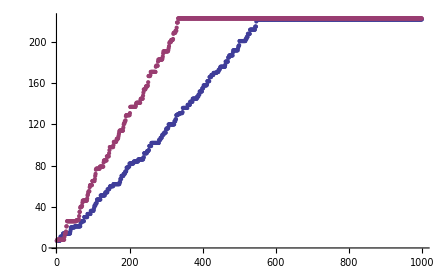

```mathematica
ListPlot[{front,frontT}]
```

```mathematica
t1=70;t2=300;
vels={LinearModelFit[front[[t1;;t2]],x,x][[1,2,2]],LinearModelFit[frontT[[t1;;t2]],x,x][[1,2,2]]}(12.5 10^-4)/(50 10^-9 10^3)
```

{9.29981,16.1628}

```mathematica
vels[[2]]/vels[[1]]
```

1.73797

```mathematica
Image[Map[1-#&,borders,{2}]]
```

-Graphics-

```mathematica
where=Map[If[#≠0,1,0]&,ind,{2}] ;
```

```mathematica
Image[where]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
indexes=Import["./output/ctags"<>ToString[700]<>".out","Table"];
```

```mathematica
borders=ArrayPad[Table[BorderQ[indexes,i,j],{i,2,399},{j,2,399}],1];
```

```mathematica
InvertONE [x_]:=1-x;
```

```mathematica
Image[Map[ColorsReplace,indexes,{2}]borders+Map[{0,0.1,0.3}#&,InvertONE/@borders,{2}]]
```

-Graphics-